# Implementación del algoritmo CAIM

### Autor: Carlos Manuel Rodríguez Martínez

Referencia: CAIM discretization algorithm, L.A. Kurgan ; K.J. Cios
DOI: 10.1109/TKDE.2004.1269594

El objetivo del algoritmo CAIM es encontrar el mínimo número de intervalos discretos que minimiza la pérdida de interdependencia entre atributo y clase.

Importar base de datos

```mathematica
data = SemanticImport[FileNameJoin[{NotebookDirectory[],"iris.csv"}]]
```

Dataset[<>]

Cálculo de matriz quanta

El algoritmo hace uso de un esquema de discretización D, con el cual se calcular la matriz Quanta, que es necesaria para obtener el valor CAIM que es la métrica que usa el algoritmo para determinar la interdependencia entre los atributos y la clase.

```mathematica
DiscretizationCount[values_,discretizationScheme_]:=Block[{intervals,firstInterval,firstIntervalCount,restIntervals,restIntervalsCount},
intervals = Partition[discretizationScheme,2,1];

firstInterval = First[intervals];
firstIntervalCount = Count[values,x_/;First[firstInterval]≤x≤Last[firstInterval]];

restIntervals = Rest[intervals];
restIntervalsCount = Map[Count[values,x_/;First[#]<x≤Last[#]]&,restIntervals];

Return[Prepend[restIntervalsCount,firstIntervalCount]];
];

QuantaMatrix[values_,class_,discretizationScheme_]:=Block[{grouped,quantaMatrix},
grouped = GroupBy[Transpose[{values,class}],Last->First];
quantaMatrix = Map[DiscretizationCount[#,discretizationScheme]&,grouped];

<|
"QuantaMatrix"->quantaMatrix, 
"Values"->Values[quantaMatrix],
"ClassTotals"->Map[Total,Values[quantaMatrix]],
"IntervalTotals"->Map[Total,Transpose[Values[quantaMatrix]]]
|>
];
```

El puntaje CAIM se determina a partir del máximo valor de la columna r de la matriz Quanta dividido por el número total de casos que pertenecen al intervalo de discretización entre (d_(r-1), d_r].

```mathematica
MaxR[m_,r_]:=Max[Part[Transpose[m],r]];

CAIMCriterion[quantaMatrix_]:=Block[{n},
n = Length[Transpose[quantaMatrix["Values"]]];

N[1/n*Sum[MaxR[quantaMatrix["Values"],r]^2/Part[quantaMatrix["IntervalTotals"],r],{r,n}]]
];

CAIMStep[values_,class_,discretizationScheme_]:=Block[{valuesAndMidpoints,BList,mutations,candidateDiscretizations},
valuesAndMidpoints = DeleteDuplicates[Sort[Join[values,Map[Mean,Partition[values,2,1]]]]];
BList = DeleteCases[DeleteDuplicates[valuesAndMidpoints],Apply[Alternatives,discretizationScheme]];
mutations = Map[Sort[Append[discretizationScheme,#]]&,BList];

candidateDiscretizations = Map[{#,Quiet@CAIMCriterion[QuantaMatrix[values,class,#]]}&,mutations];
candidateDiscretizations = DeleteCases[candidateDiscretizations,{_,Indeterminate}];

First[MaximalBy[candidateDiscretizations,Last]]
];
```

### Ejemplo:

A continuación se seleccionan como valores todas las entradas de la base de datos correspondientes a la longitud del sépalo.

```mathematica
values = Normal@data[All,"Sepal length"]
```

{5.1,4.9,4.7,4.6,5.,5.4,4.6,5.,4.4,4.9,5.4,4.8,4.8,4.3,5.8,5.7,5.4,5.1,5.7,5.1,5.4,5.1,4.6,5.1,4.8,5.,5.,5.2,5.2,4.7,4.8,5.4,5.2,5.5,4.9,5.,5.5,4.9,4.4,5.1,5.,4.5,4.4,5.,5.1,4.8,5.1,4.6,5.3,5.,7.,6.4,6.9,5.5,6.5,5.7,6.3,4.9,6.6,5.2,5.,5.9,6.,6.1,5.6,6.7,5.6,5.8,6.2,5.6,5.9,6.1,6.3,6.1,6.4,6.6,6.8,6.7,6.,5.7,5.5,5.5,5.8,6.,5.4,6.,6.7,6.3,5.6,5.5,5.5,6.1,5.8,5.,5.6,5.7,5.7,6.2,5.1,5.7,6.3,5.8,7.1,6.3,6.5,7.6,4.9,7.3,6.7,7.2,6.5,6.4,6.8,5.7,5.8,6.4,6.5,7.7,7.7,6.,6.9,5.6,7.7,6.3,6.7,7.2,6.2,6.1,6.4,7.2,7.4,7.9,6.4,6.3,6.1,7.7,6.3,6.4,6.,6.9,6.7,6.9,5.8,6.8,6.7,6.7,6.3,6.5,6.2,5.9}

```mathematica
class = Normal@data[All,"Class"]
```

{Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica}

Se comienza con un esquema de discretización en el intervalo entre el mínimo y máximo valor del atributo a discretizar. Esto es un esq	uema de discretización donde todos los valores caen dentro del mismo intervalo.

```mathematica
scheme = MinMax[values]
```

{4.3,7.9}

Visualización del esquema de discretización. Las líneas verticales representan el mínimo y máximo valor del atributo.

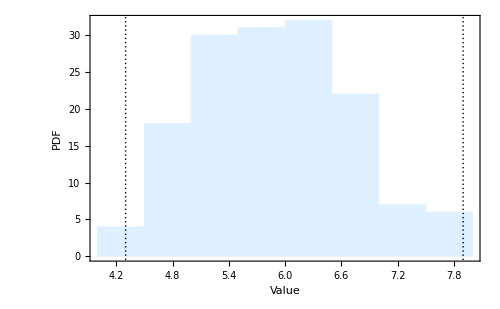

```mathematica
Histogram[
values,
PlotTheme->"Monochrome", 
FrameLabel->{Style["Value",15], Style["PDF",15]},
BaseStyle->FontSize->13,
ImageSize->500,
ChartStyle->LightBlue,
GridLines->{scheme,{}},
FrameTicks->True,
Frame->True
]
```

Inicialmente todos los valores caen dentro del mismo intervalo

```mathematica
DiscretizationCount[values,{4.3,7.9}]
```

{150}

```mathematica
DeleteDuplicates[Sort[values]]
```

{4.3,4.4,4.5,4.6,4.7,4.8,4.9,5.,5.1,5.2,5.3,5.4,5.5,5.6,5.7,5.8,5.9,6.,6.1,6.2,6.3,6.4,6.5,6.6,6.7,6.8,6.9,7.,7.1,7.2,7.3,7.4,7.6,7.7,7.9}

El algoritmo CAIM selecciona de entre la lista de posibles particiones del esquema de discretización.

```mathematica
B = DeleteCases[DeleteDuplicates[Sort[Join[values,Map[Mean,Partition[values,2,1]]]]],Apply[Alternatives,scheme]]
```

{4.4,4.45,4.5,4.55,4.6,4.65,4.7,4.75,4.8,4.8,4.85,4.9,4.95,4.95,5.,5.05,5.1,5.15,5.2,5.25,5.3,5.3,5.35,5.4,5.45,5.5,5.55,5.55,5.6,5.65,5.7,5.7,5.75,5.8,5.85,5.9,5.95,5.95,6.,6.05,6.05,6.1,6.15,6.2,6.2,6.25,6.3,6.35,6.4,6.45,6.45,6.5,6.6,6.65,6.7,6.7,6.75,6.8,6.8,6.85,6.9,6.95,7.,7.05,7.1,7.15,7.2,7.3,7.3,7.4,7.6,7.65,7.7}

Con esto es capaz de construir una tabla de posibles valores del esquema de discretización

```mathematica
Map[Sort[Append[scheme,#]]&,B]
```

{{4.3,4.4,7.9},{4.3,4.45,7.9},{4.3,4.5,7.9},{4.3,4.55,7.9},{4.3,4.6,7.9},{4.3,4.65,7.9},{4.3,4.7,7.9},{4.3,4.75,7.9},{4.3,4.8,7.9},{4.3,4.8,7.9},{4.3,4.85,7.9},{4.3,4.9,7.9},{4.3,4.95,7.9},{4.3,4.95,7.9},{4.3,5.,7.9},{4.3,5.05,7.9},{4.3,5.1,7.9},{4.3,5.15,7.9},{4.3,5.2,7.9},{4.3,5.25,7.9},{4.3,5.3,7.9},{4.3,5.3,7.9},{4.3,5.35,7.9},{4.3,5.4,7.9},{4.3,5.45,7.9},{4.3,5.5,7.9},{4.3,5.55,7.9},{4.3,5.55,7.9},{4.3,5.6,7.9},{4.3,5.65,7.9},{4.3,5.7,7.9},{4.3,5.7,7.9},{4.3,5.75,7.9},{4.3,5.8,7.9},{4.3,5.85,7.9},{4.3,5.9,7.9},{4.3,5.95,7.9},{4.3,5.95,7.9},{4.3,6.,7.9},{4.3,6.05,7.9},{4.3,6.05,7.9},{4.3,6.1,7.9},{4.3,6.15,7.9},{4.3,6.2,7.9},{4.3,6.2,7.9},{4.3,6.25,7.9},{4.3,6.3,7.9},{4.3,6.35,7.9},{4.3,6.4,7.9},{4.3,6.45,7.9},{4.3,6.45,7.9},{4.3,6.5,7.9},{4.3,6.6,7.9},{4.3,6.65,7.9},{4.3,6.7,7.9},{4.3,6.7,7.9},{4.3,6.75,7.9},{4.3,6.8,7.9},{4.3,6.8,7.9},{4.3,6.85,7.9},{4.3,6.9,7.9},{4.3,6.95,7.9},{4.3,7.,7.9},{4.3,7.05,7.9},{4.3,7.1,7.9},{4.3,7.15,7.9},{4.3,7.2,7.9},{4.3,7.3,7.9},{4.3,7.3,7.9},{4.3,7.4,7.9},{4.3,7.6,7.9},{4.3,7.65,7.9},{4.3,7.7,7.9}}

De esta lista selecciona el valor que maximiza el puntaje de CAIM

```mathematica
CAIMStep[values,class,scheme]
```

{{4.3,5.5,7.9},31.9126}

Esto da como resultado un esquema donde 59 ejemplos caen en el intervalo [4.3, 5.5], y 91 en el intervalo (5.5,7.9].

```mathematica
DiscretizationCount[values,{4.3,5.5,7.9}]
```

{59,91}

y que da la siguiente matriz Quanta

```mathematica
QuantaMatrix[values,class,{4.3,5.5,7.9}]
```

<|QuantaMatrix→<|Iris-setosa→{47,3},Iris-versicolor→{11,39},Iris-virginica→{1,49}|>,Values→{{47,3},{11,39},{1,49}},ClassTotals→{50,50,50},IntervalTotals→{59,91}|>

```mathematica
MatrixForm[QuantaMatrix[values,class,{4.3,5.5,7.9}]["Values"]]
```

(47 | 3
11 | 39
1 | 49)

Este proceso se puede repetir varias veces.

```mathematica
CAIMStep[values,class,{4.3,5.5,7.9}]
```

{{4.3,5.5,6.2,7.9},26.6363}

```mathematica
CAIMStep[values,class,{4.3,5.5,6.2,7.9}]
```

{{4.3,5.4,5.5,6.2,7.9},21.2455}

Algoritmo principal

A continuación se implementa el algoritmo principal tal como se describe en el artículo. Asimismo se implementa una función que aplica la discretización a toda la base de datos.

```mathematica
CAIMAlgorithm[values_,class_,maxIterations_ :100]:=Block[{scheme,F,GlobalCAIM,k,CAIMScore,classes,caimResults},
scheme = MinMax[values];
classes = Length[DeleteDuplicates[class]];
F = Sort[values];
GlobalCAIM = 0;
CAIMScore = 0;
caimResults = {};

k = 1;
While[k<maxIterations,
{scheme,CAIMScore}= CAIMStep[values,class,scheme];
If[CAIMScore>GlobalCAIM|| k<classes,
AppendTo[caimResults,{scheme,CAIMScore}];
GlobalCAIM = CAIMScore;
,
Return[caimResults];
];
k++;
]
];

CAIMDiscretize[values_,class_]:=Block[{caimScheme,parts,discretizationRule},
caimScheme = First[Last[CAIMAlgorithm[values,class]]];
parts = Partition[caimScheme,2,1];

discretizationRule = MapIndexed[
If[First[#2] == 1,
x_ /; First[#1]≤x≤Last[#1]->First[#2]-1,
x_ /; First[#1]<x≤Last[#1]->First[#2]-1
]&,
parts
];

ReplaceAll[values, discretizationRule]
];

CAIMDatabaseDiscretize[database_]:=Block[{class,keys,discretized,discretizedRawDatabase},
class = Normal@database[All,"Class"];
keys = Keys[First[Normal[database]]];
discretized = Map[CAIMDiscretize[Normal@database[All,#],class]&,DeleteCases[keys,"Class"]];
discretizedRawDatabase = Transpose@Join[discretized,{Normal@database[All,"Class"]}];

Dataset[Map[Association[Thread[keys->#]]&,discretizedRawDatabase]]
];
```

### Ejemplo:

CAIMAlgorithm ejecuta el algoritmo CAIM mostrando el puntaje en cada iteración.

```mathematica
CAIMAlgorithm[values,class]
```

{{{4.3,5.5,7.9},31.9126},{{4.3,5.5,6.2,7.9},26.6363}}

```mathematica
CAIMStep[values,class,{4.3,5.5,6.2,7.9}]
```

{{4.3,5.4,5.5,6.2,7.9},21.2455}

```mathematica
QuantaMatrix[values,class,{4.3,5.5,7.9}]
```

<|QuantaMatrix→<|Iris-setosa→{47,3},Iris-versicolor→{11,39},Iris-virginica→{1,49}|>,Values→{{47,3},{11,39},{1,49}},ClassTotals→{50,50,50},IntervalTotals→{59,91}|>

```mathematica
QuantaMatrix[values,class,{4.3,5.5,6.2,7.9}]
```

<|QuantaMatrix→<|Iris-setosa→{47,3,0},Iris-versicolor→{11,25,14},Iris-virginica→{1,12,37}|>,Values→{{47,3,0},{11,25,14},{1,12,37}},ClassTotals→{50,50,50},IntervalTotals→{59,40,51}|>

CAIMDiscretize discretiza un solo atributo.

```mathematica
values
```

{5.1,4.9,4.7,4.6,5.,5.4,4.6,5.,4.4,4.9,5.4,4.8,4.8,4.3,5.8,5.7,5.4,5.1,5.7,5.1,5.4,5.1,4.6,5.1,4.8,5.,5.,5.2,5.2,4.7,4.8,5.4,5.2,5.5,4.9,5.,5.5,4.9,4.4,5.1,5.,4.5,4.4,5.,5.1,4.8,5.1,4.6,5.3,5.,7.,6.4,6.9,5.5,6.5,5.7,6.3,4.9,6.6,5.2,5.,5.9,6.,6.1,5.6,6.7,5.6,5.8,6.2,5.6,5.9,6.1,6.3,6.1,6.4,6.6,6.8,6.7,6.,5.7,5.5,5.5,5.8,6.,5.4,6.,6.7,6.3,5.6,5.5,5.5,6.1,5.8,5.,5.6,5.7,5.7,6.2,5.1,5.7,6.3,5.8,7.1,6.3,6.5,7.6,4.9,7.3,6.7,7.2,6.5,6.4,6.8,5.7,5.8,6.4,6.5,7.7,7.7,6.,6.9,5.6,7.7,6.3,6.7,7.2,6.2,6.1,6.4,7.2,7.4,7.9,6.4,6.3,6.1,7.7,6.3,6.4,6.,6.9,6.7,6.9,5.8,6.8,6.7,6.7,6.3,6.5,6.2,5.9}

```mathematica
CAIMDiscretize[values,class]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,2,0,2,1,2,0,2,0,0,1,1,1,1,2,1,1,1,1,1,1,2,1,2,2,2,2,1,1,0,0,1,1,0,1,2,2,1,0,0,1,1,0,1,1,1,1,0,1,2,1,2,2,2,2,0,2,2,2,2,2,2,1,1,2,2,2,2,1,2,1,2,2,2,2,1,1,2,2,2,2,2,2,1,2,2,2,1,2,2,2,1,2,2,2,2,2,1,1}

CAIMDatabaseDiscretize discretiza toda la base de datos.

```mathematica
CAIMDatabaseDiscretize[data]
```

Dataset[<>]

Exportación de base de datos discretizada

```mathematica
Values@Normal[CAIMDatabaseDiscretize[data]]
```

{{0,2,0,0,Iris-setosa},{0,1,0,0,Iris-setosa},{0,2,0,0,Iris-setosa},{0,2,0,0,Iris-setosa},{0,2,0,0,Iris-setosa},{0,2,0,0,Iris-setosa},{0,2,0,0,Iris-setosa},{0,2,0,0,Iris-setosa},{0,0,0,0,Iris-setosa},{0,2,0,0,Iris-setosa},{0,2,0,0,Iris-setosa},{0,2,0,0,Iris-setosa},{0,1,0,0,Iris-setosa},{0,1,0,0,Iris-setosa},{1,2,0,0,Iris-setosa},{1,2,0,0,Iris-setosa},{0,2,0,0,Iris-setosa},{0,2,0,0,Iris-setosa},{1,2,0,0,Iris-setosa},{0,2,0,0,Iris-setosa},{0,2,0,0,Iris-setosa},{0,2,0,0,Iris-setosa},{0,2,0,0,Iris-setosa},{0,2,0,0,Iris-setosa},{0,2,0,0,Iris-setosa},{0,1,0,0,Iris-setosa},{0,2,0,0,Iris-setosa},{0,2,0,0,Iris-setosa},{0,2,0,0,Iris-setosa},{0,2,0,0,Iris-setosa},{0,2,0,0,Iris-setosa},{0,2,0,0,Iris-setosa},{0,2,0,0,Iris-setosa},{0,2,0,0,Iris-setosa},{0,2,0,0,Iris-setosa},{0,2,0,0,Iris-setosa},{0,2,0,0,Iris-setosa},{0,2,0,0,Iris-setosa},{0,1,0,0,Iris-setosa},{0,2,0,0,Iris-setosa},{0,2,0,0,Iris-setosa},{0,0,0,0,Iris-setosa},{0,2,0,0,Iris-setosa},{0,2,0,0,Iris-setosa},{0,2,0,0,Iris-setosa},{0,1,0,0,Iris-setosa},{0,2,0,0,Iris-setosa},{0,2,0,0,Iris-setosa},{0,2,0,0,Iris-setosa},{0,2,0,0,Iris-setosa},{2,2,1,1,Iris-versicolor},{2,2,1,1,Iris-versicolor},{2,2,2,1,Iris-versicolor},{0,0,1,1,Iris-versicolor},{2,0,1,1,Iris-versicolor},{1,0,1,1,Iris-versicolor},{2,2,1,1,Iris-versicolor},{0,0,1,1,Iris-versicolor},{2,0,1,1,Iris-versicolor},{0,0,1,1,Iris-versicolor},{0,0,1,1,Iris-versicolor},{1,1,1,1,Iris-versicolor},{1,0,1,1,Iris-versicolor},{1,0,1,1,Iris-versicolor},{1,0,1,1,Iris-versicolor},{2,2,1,1,Iris-versicolor},{1,1,1,1,Iris-versicolor},{1,0,1,1,Iris-versicolor},{1,0,1,1,Iris-versicolor},{1,0,1,1,Iris-versicolor},{1,2,2,2,Iris-versicolor},{1,0,1,1,Iris-versicolor},{2,0,2,1,Iris-versicolor},{1,0,1,1,Iris-versicolor},{2,0,1,1,Iris-versicolor},{2,1,1,1,Iris-versicolor},{2,0,2,1,Iris-versicolor},{2,1,2,1,Iris-versicolor},{1,0,1,1,Iris-versicolor},{1,0,1,1,Iris-versicolor},{0,0,1,1,Iris-versicolor},{0,0,1,1,Iris-versicolor},{1,0,1,1,Iris-versicolor},{1,0,2,1,Iris-versicolor},{0,1,1,1,Iris-versicolor},{1,2,1,1,Iris-versicolor},{2,2,1,1,Iris-versicolor},{2,0,1,1,Iris-versicolor},{1,1,1,1,Iris-versicolor},{0,0,1,1,Iris-versicolor},{0,0,1,1,Iris-versicolor},{1,1,1,1,Iris-versicolor},{1,0,1,1,Iris-versicolor},{0,0,1,1,Iris-versicolor},{1,0,1,1,Iris-versicolor},{1,1,1,1,Iris-versicolor},{1,0,1,1,Iris-versicolor},{1,0,1,1,Iris-versicolor},{0,0,1,1,Iris-versicolor},{1,0,1,1,Iris-versicolor},{2,2,2,2,Iris-virginica},{1,0,2,2,Iris-virginica},{2,1,2,2,Iris-virginica},{2,0,2,2,Iris-virginica},{2,1,2,2,Iris-virginica},{2,1,2,2,Iris-virginica},{0,0,1,1,Iris-virginica},{2,0,2,2,Iris-virginica},{2,0,2,2,Iris-virginica},{2,2,2,2,Iris-virginica},{2,2,2,2,Iris-virginica},{2,0,2,2,Iris-virginica},{2,1,2,2,Iris-virginica},{1,0,2,2,Iris-virginica},{1,0,2,2,Iris-virginica},{2,2,2,2,Iris-virginica},{2,1,2,2,Iris-virginica},{2,2,2,2,Iris-virginica},{2,0,2,2,Iris-virginica},{1,0,2,1,Iris-virginica},{2,2,2,2,Iris-virginica},{1,0,2,2,Iris-virginica},{2,0,2,2,Iris-virginica},{2,0,2,2,Iris-virginica},{2,2,2,2,Iris-virginica},{2,2,2,2,Iris-virginica},{1,0,2,2,Iris-virginica},{1,1,2,2,Iris-virginica},{2,0,2,2,Iris-virginica},{2,1,2,1,Iris-virginica},{2,0,2,2,Iris-virginica},{2,2,2,2,Iris-virginica},{2,0,2,2,Iris-virginica},{2,0,2,1,Iris-virginica},{1,0,2,1,Iris-virginica},{2,1,2,2,Iris-virginica},{2,2,2,2,Iris-virginica},{2,2,2,2,Iris-virginica},{1,1,2,2,Iris-virginica},{2,2,2,2,Iris-virginica},{2,2,2,2,Iris-virginica},{2,2,2,2,Iris-virginica},{1,0,2,2,Iris-virginica},{2,2,2,2,Iris-virginica},{2,2,2,2,Iris-virginica},{2,1,2,2,Iris-virginica},{2,0,2,2,Iris-virginica},{2,1,2,2,Iris-virginica},{1,2,2,2,Iris-virginica},{1,1,2,2,Iris-virginica}}

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"discretizada.csv"}],Values@Normal[CAIMDatabaseDiscretize[data]]]
```

/home/carlos/Documentos/Programacion/Fisica-Mathematica/Machine_Learning/CAIM/discretizada.csv